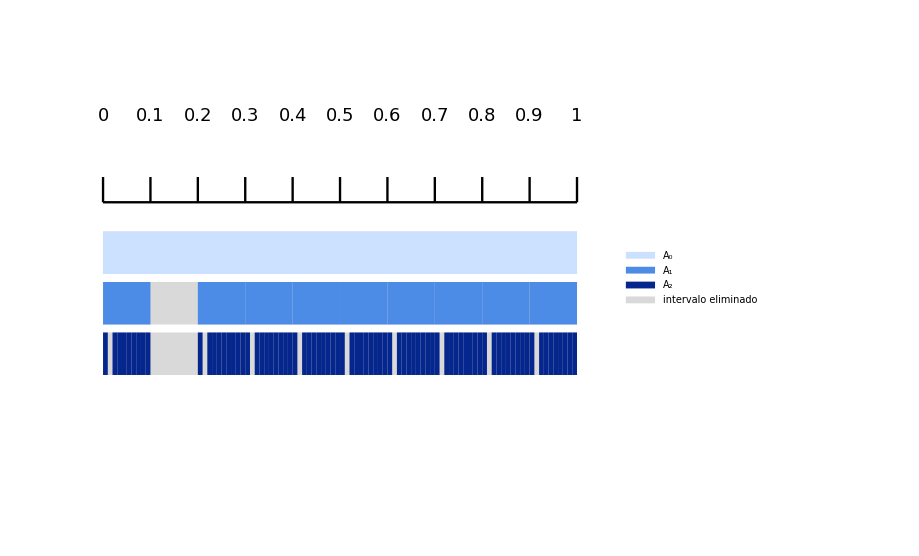

```mathematica
ClearAll[digitosPermitidos,generarIntervalos,nMax,sep,axisY,colores,etiquetas,etiquetasEjeX,ejeX,fondo,barras,grafico,imagenFinal];

digitosPermitidos={0,2,3,4,5,6,7,8,9};   (*todas las cifras salvo el 1*)

generarIntervalos[0]:={{0,1}};
generarIntervalos[n_]:=Module[{combinaciones=Tuples[digitosPermitidos,n]},Function[digitos,With[{inicio=Sum[digitos[[i]] 10^-i,{i,n}]},{inicio,inicio+10^-n}]]/@combinaciones];

nMax=2;
sep=0.1;    (*separación vertical entre A_n consecutivos*)
axisY=0.1;   (*altura de la recta real,pegada a A_0*)
colores={RGBColor[0.8,0.88,1],RGBColor[0.3,0.55,0.9],RGBColor[0.02,0.15,0.55]};
etiquetas={"A₀","A₁","A₂"};

etiquetasEjeX=Table[Which[k==0,"0",k==10,"1",True,"0."<>ToString[k]],{k,0,10}];

ejeX={Black,Thickness[0.0025],Line[{{0,axisY},{1,axisY}}],Table[Line[{{k/10,axisY},{k/10,axisY+0.05}}],{k,0,10}],Table[Text[Style[etiquetasEjeX[[k+1]],18],{k/10,axisY+0.17}],{k,0,10}]};

fondo=Table[{LightGray,Thickness[0.045],CapForm["Butt"],Line[{{0,-n sep},{1,-n sep}}]},{n,0,nMax}];

barras=Table[Module[{intervalos=generarIntervalos[n],y=-n sep},{colores[[n+1]],Thickness[0.045],CapForm["Butt"],Line[{{#[[1]],y},{#[[2]],y}}]&/@intervalos}],{n,0,nMax}];

grafico=Graphics[{ejeX,fondo,barras},PlotRange->{{-0.05,1.05},{-nMax sep-0.3,axisY+0.3}},ImageSize->680];

imagenFinal=Legended[grafico,SwatchLegend[Append[colores,LightGray],Append[etiquetas,"intervalo eliminado"],LabelStyle->Directive[FontSize->20],LegendMarkerSize->22]];

imagenFinal
```

```mathematica
Export["T2_P28_a.png",imagenFinal,Background->None,ImageResolution->300];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["T2_P28_a.png"]]]
```

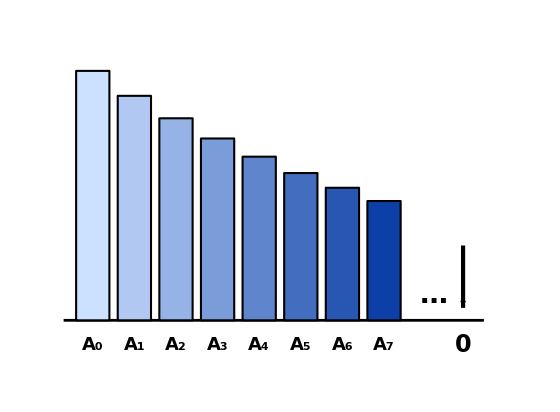

```mathematica
ClearAll[nB,esc,colBarra,barras,etiquetasX,base,puntos,flechaCero,diagrama2];

nB=8;esc=6;
colBarra[n_]:=Blend[{RGBColor[0.8,0.88,1],RGBColor[0.05,0.25,0.65]},n/(nB-1)];

(*la altura de cada barra es la medida del conjunto:cada paso conserva 9/10 de la anterior*)
barras=Table[{colBarra[n],EdgeForm[{Black,AbsoluteThickness[1.5]}],Rectangle[{n+1-0.4,0},{n+1+0.4,esc (9/10)^n}]},{n,0,nB-1}];

etiquetasX=Table[Text[Style[Subscript["A",n],18,Bold],{n+1,-0.6}],{n,0,nB-1}];

base={Black,AbsoluteThickness[2],Line[{{0.3,0},{nB+2.4,0}}]};

puntos=Text[Style["…",28,Bold],{nB+1.2,0.6}];

flechaCero={Black,AbsoluteThickness[3],Arrowheads[0.05],Arrow[{{nB+1.9,1.8},{nB+1.9,0.3}}],Text[Style["0",24,Bold],{nB+1.9,-0.6}]};

diagrama2=Graphics[{base,barras,etiquetasX,puntos,flechaCero},PlotRange->{{0,nB+3},{-1.3,esc+0.8}},ImageSize->560];

diagrama2

Export["prob28_b_medida.png",diagrama2,Background->White,ImageResolution->300];
```

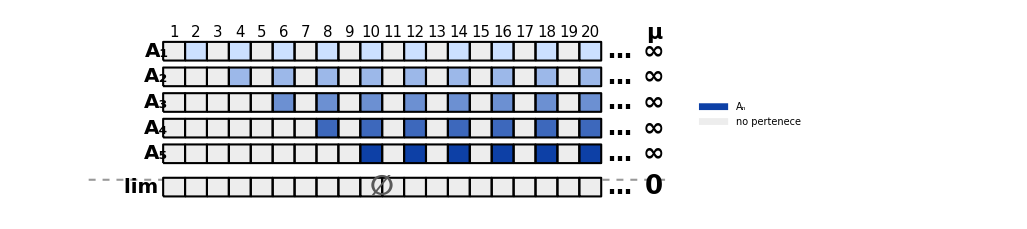

```mathematica
ClearAll[nTot,nFilas,dy,colFila,colNo,celda,filaA,cabecera,yLast,ySep,yLim,separador,filaLim,grafico3,diagrama3];

nTot=20;nFilas=5;dy=1.1;
colFila[n_]:=Blend[{RGBColor[0.8,0.88,1],RGBColor[0.05,0.25,0.65]},(n-1)/(nFilas-1)];
colNo=GrayLevel[0.93];

celda[k_,y_,col_]:={col,EdgeForm[{Black,AbsoluteThickness[1.5]}],Rectangle[{k-1,y},{k,y+0.8}]};

(*A_n={2n,2n+2,2n+4,...}:los pares a partir de 2n*)
filaA[n_]:=With[{y=-(n-1) dy},{Table[celda[k,y,If[EvenQ[k]&&k>=2 n,colFila[n],colNo]],{k,1,nTot}],Black,Text[Style[Subscript["A",n],20,Bold],{-0.3,y+0.4},{1,0}],Text[Style["…",24,Bold],{nTot+0.8,y+0.4}],Text[Style["∞",26,Bold],{nTot+2.4,y+0.4}]}];

cabecera={Table[Text[Style[k,15],{k-0.5,1.2}],{k,1,nTot}],Text[Style["μ",22,Bold],{nTot+2.4,1.2}]};

yLast=-(nFilas-1) dy;
ySep=yLast-0.65 dy;
yLim=yLast-1.3 dy;

separador={GrayLevel[0.6],Dashed,AbsoluteThickness[1.5],Line[{{-3.4,ySep},{nTot+3.2,ySep}}]};

(*el límite es el vacío:ninguna casilla coloreada*)
filaLim={Table[celda[k,yLim,colNo],{k,1,nTot}],Black,Text[Style[Row[{"lim ",Subscript["A","n"]}],20,Bold],{-0.3,yLim+0.4},{1,0}],Text[Style["∅",28,Bold,GrayLevel[0.35]],{nTot/2,yLim+0.4}],Text[Style["…",24,Bold],{nTot+0.8,yLim+0.4}],Text[Style["0",26,Bold],{nTot+2.4,yLim+0.4}]};

grafico3=Graphics[{cabecera,Table[filaA[n],{n,1,nFilas}],separador,filaLim},PlotRange->{{-3.4,nTot+3.2},{yLim-0.5,1.7}},ImageSize->760];

diagrama3=Legended[grafico3,SwatchLegend[{colFila[nFilas],colNo},{Subscript["A","n"],"no pertenece"},LabelStyle->Directive[FontSize->17],LegendMarkerSize->20]];

diagrama3

Export["T2_P29_a.png",diagrama3,Background->None,ImageResolution->300];
```

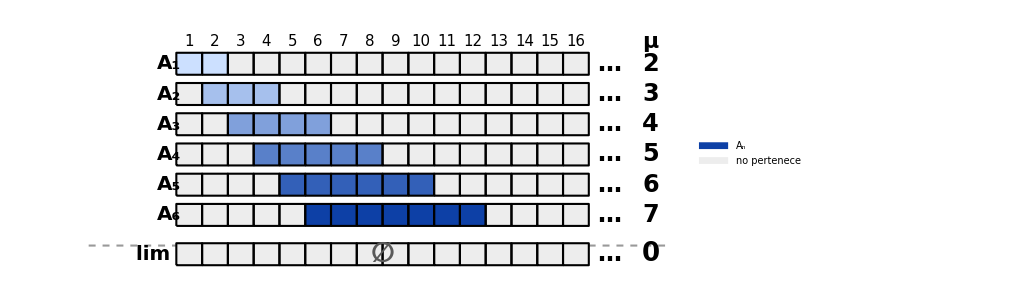

```mathematica
ClearAll[nTot,nFilas,dy,colFila,colNo,celda,filaA,cabecera,yLast,ySep,yLim,separador,filaLim,grafico4,diagrama4];

nTot=16;nFilas=6;dy=1.1;
colFila[n_]:=Blend[{RGBColor[0.8,0.88,1],RGBColor[0.05,0.25,0.65]},(n-1)/(nFilas-1)];
colNo=GrayLevel[0.93];

celda[k_,y_,col_]:={col,EdgeForm[{Black,AbsoluteThickness[1.5]}],Rectangle[{k-1,y},{k,y+0.8}]};

(*A_n={n,n+1,...,2n};a la derecha,su número de elementos*)
filaA[n_]:=With[{y=-(n-1) dy},{Table[celda[k,y,If[n<=k<=2 n,colFila[n],colNo]],{k,1,nTot}],Black,Text[Style[Subscript["A",n],20,Bold],{-0.3,y+0.4},{1,0}],Text[Style["…",24,Bold],{nTot+0.8,y+0.4}],Text[Style[n+1,24,Bold],{nTot+2.4,y+0.4}]}];

cabecera={Table[Text[Style[k,15],{k-0.5,1.2}],{k,1,nTot}],Text[Style["μ",22,Bold],{nTot+2.4,1.2}]};

yLast=-(nFilas-1) dy;
ySep=yLast-0.65 dy;
yLim=yLast-1.3 dy;

separador={GrayLevel[0.6],Dashed,AbsoluteThickness[1.5],Line[{{-3.4,ySep},{nTot+3.2,ySep}}]};

(*el límite es el vacío:ningún número se queda en la ventana*)
filaLim={Table[celda[k,yLim,colNo],{k,1,nTot}],Black,Text[Style[Row[{"lim ",Subscript["A","n"]}],20,Bold],{-0.3,yLim+0.4},{1,0}],Text[Style["∅",28,Bold,GrayLevel[0.35]],{nTot/2,yLim+0.4}],Text[Style["…",24,Bold],{nTot+0.8,yLim+0.4}],Text[Style["0",26,Bold],{nTot+2.4,yLim+0.4}]};

grafico4=Graphics[{cabecera,Table[filaA[n],{n,1,nFilas}],separador,filaLim},PlotRange->{{-3.4,nTot+3.2},{yLim-0.5,1.7}},ImageSize->760];

diagrama4=Legended[grafico4,SwatchLegend[{colFila[nFilas],colNo},{Subscript["A","n"],"no pertenece"},LabelStyle->Directive[FontSize->17],LegendMarkerSize->20]];

diagrama4

Export["T2_P29_b.png",diagrama4,Background->None,ImageResolution->600];
```

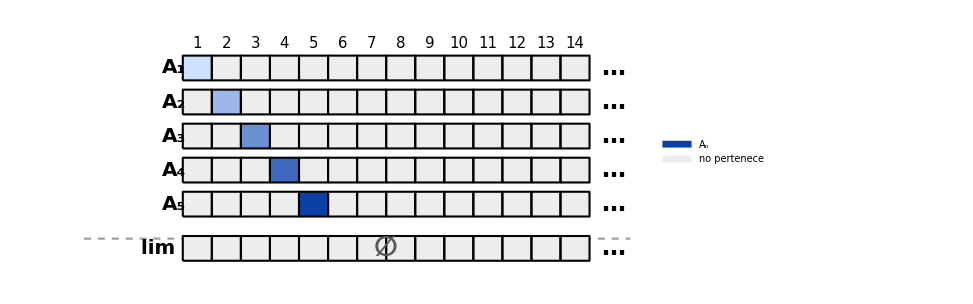

```mathematica
ClearAll[nTot,nFilas,dy,colFila,colNo,celda,filaA,cabecera,yLast,ySep,yLim,separador,filaLim,grafico1,diagrama1];

nTot=14;nFilas=5;dy=1.1;
colFila[n_]:=Blend[{RGBColor[0.8,0.88,1],RGBColor[0.05,0.25,0.65]},(n-1)/(nFilas-1)];
colNo=GrayLevel[0.93];

celda[k_,y_,col_]:={col,EdgeForm[{Black,AbsoluteThickness[1.5]}],Rectangle[{k-1,y},{k,y+0.8}]};

(*A_n={n}:una sola casilla coloreada por fila,que avanza hacia la derecha*)
filaA[n_]:=With[{y=-(n-1) dy},{Table[celda[k,y,If[k==n,colFila[n],colNo]],{k,1,nTot}],Black,Text[Style[Subscript["A",n],20,Bold],{-0.3,y+0.4},{1,0}],Text[Style["…",24,Bold],{nTot+0.8,y+0.4}]}];

cabecera=Table[Text[Style[k,15],{k-0.5,1.2}],{k,1,nTot}];

yLast=-(nFilas-1) dy;
ySep=yLast-0.65 dy;
yLim=yLast-1.3 dy;

separador={GrayLevel[0.6],Dashed,AbsoluteThickness[1.5],Line[{{-3.4,ySep},{nTot+1.4,ySep}}]};

(*el límite es el vacío:ninguna casilla coloreada*)
filaLim={Table[celda[k,yLim,colNo],{k,1,nTot}],Black,Text[Style[Row[{"lim ",Subscript["A","n"]}],20,Bold],{-0.3,yLim+0.4},{1,0}],Text[Style["∅",28,Bold,GrayLevel[0.35]],{nTot/2,yLim+0.4}],Text[Style["…",24,Bold],{nTot+0.8,yLim+0.4}]};

grafico1=Graphics[{cabecera,Table[filaA[n],{n,1,nFilas}],separador,filaLim},PlotRange->{{-3.4,nTot+1.6},{yLim-0.5,1.7}},ImageSize->720];

diagrama1=Legended[grafico1,SwatchLegend[{colFila[nFilas],colNo},{Subscript["A","n"],"no pertenece"},LabelStyle->Directive[FontSize->17],LegendMarkerSize->20]];

diagrama1

Export["T2_P30_sucesion.png",diagrama1,Background->None,ImageResolution->600];
```

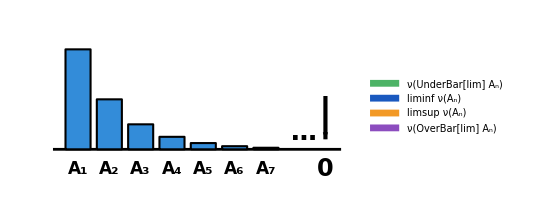
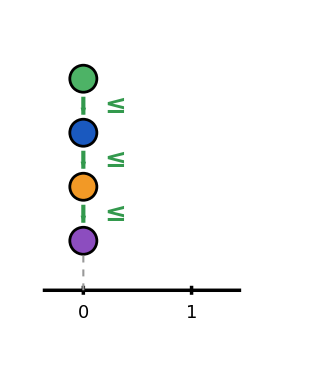
ν(A_n)
-Graphics-Cadena de desigualdades
-Graphics-

```mathematica
ClearAll[nB,esc,colBar,colP,xEsc,yP,flechaEntre,cadena,panelBarras,columnaIzq,columnaDer,leyenda,diagrama2];

nB=7;esc=6;
colBar=RGBColor[0.2,0.55,0.85];
colP={RGBColor[0.3,0.7,0.4],RGBColor[0.1,0.35,0.75],RGBColor[0.95,0.6,0.15],RGBColor[0.55,0.3,0.75]};
xEsc=2.4;                 (*escala horizontal:el valor 1 queda en x=xEsc*)
yP={3.6,2.4,1.2,0};    (*de arriba abajo,en el orden de la cadena*)

(*flecha entre dos eslabones;si no se cumple,va en rojo y con el signo tachado*)
flechaEntre[p_,q_,ok_]:=Module[{u,a,b,m,c},u=Normalize[q-p];
a=p+0.4 u;b=q-0.4 u;
m=(a+b)/2+{0.7,0};
c=If[ok,RGBColor[0.2,0.6,0.3],RGBColor[0.8,0.15,0.2]];
{c,AbsoluteThickness[3],Arrowheads[0.05],Arrow[{a,b}],Text[Style["≤",26,Bold,c],m],If[ok,{},{AbsoluteThickness[4],Line[{m+{-0.28,-0.32},m+{0.28,0.32}}]}]}];

cadena[vals_List,oks_List]:=Module[{pts,guias},pts=Table[{xEsc vals[[k]],yP[[k]]},{k,4}];
guias=Table[{GrayLevel[0.6],Dashed,AbsoluteThickness[1.5],Line[{{xv,-1.1},{xv,Min[Select[pts,First[#]==xv&][[All,2]]]-0.3}}]},{xv,DeleteDuplicates[pts[[All,1]]]}];
Graphics[{{Black,AbsoluteThickness[2.5],Line[{{-0.9,-1.1},{xEsc+1.1,-1.1}}],Line[{{0,-1.0},{0,-1.2}}],Line[{{xEsc,-1.0},{xEsc,-1.2}}],Text[Style["0",18],{0,-1.6}],Text[Style["1",18],{xEsc,-1.6}]},guias,Table[flechaEntre[pts[[k]],pts[[k+1]],oks[[k]]],{k,3}],Table[{colP[[k]],EdgeForm[{Black,AbsoluteThickness[2]}],Disk[pts[[k]],0.3]},{k,4}]},PlotRange->{{-1.2,xEsc+2.2},{-2.1,yP[[1]]+1}},ImageSize->320]];

(*barras de nu(A_n)=nu({n}):ejemplo ilustrativo que decrece hasta 0*)
panelBarras=Graphics[{{Black,AbsoluteThickness[2],Line[{{0.2,0},{nB+2.4,0}}]},Table[{colBar,EdgeForm[{Black,AbsoluteThickness[1.5]}],Rectangle[{n-0.4,0},{n+0.4,esc 2^-n}]},{n,1,nB}],Table[Text[Style[Subscript["A",n],17,Bold],{n,-0.6}],{n,1,nB}],Text[Style["…",26,Bold],{nB+1.2,0.5}],{Black,AbsoluteThickness[3],Arrowheads[0.05],Arrow[{{nB+1.9,1.6},{nB+1.9,0.3}}],Text[Style["0",24,Bold],{nB+1.9,-0.6}]}},PlotRange->{{0,nB+2.8},{-1.3,esc/2+0.9}},ImageSize->400];

columnaIzq=Column[{Style[Row[{"ν(",Subscript["A","n"],")"}],20,Bold],panelBarras},Alignment->Center,Spacings->0.5];
columnaDer=Column[{Style["Cadena de desigualdades",20,Bold],cadena[{0,0,0,0},{True,True,True}]},Alignment->Center,Spacings->0.5];

leyenda=SwatchLegend[colP,{Row[{"ν(",UnderBar["lim"]," ",Subscript["A","n"],")"}],Row[{"liminf ν(",Subscript["A","n"],")"}],Row[{"limsup ν(",Subscript["A","n"],")"}],Row[{"ν(",OverBar["lim"]," ",Subscript["A","n"],")"}]},LabelStyle->Directive[FontSize->17],LegendMarkerSize->20];

diagrama2=Legended[Row[{columnaIzq,Spacer[40],columnaDer}],leyenda];

diagrama2

Export["T2_P30_a.png",diagrama2,Background->None,ImageResolution->600];
```

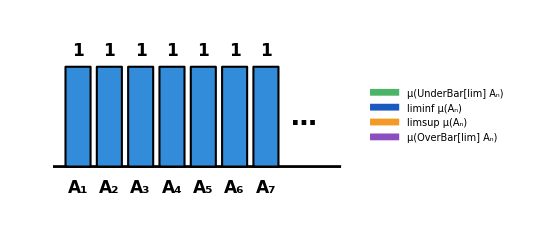
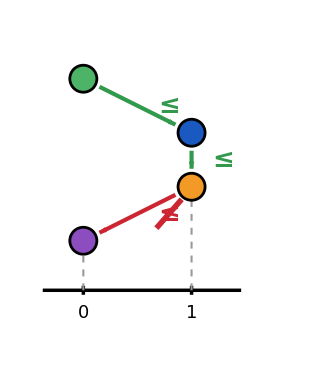
μ(A_n)
-Graphics-Cadena de desigualdades
-Graphics-

```mathematica
ClearAll[nB,esc,colBar,colP,xEsc,yP,flechaEntre,cadena,panelBarras,columnaIzq,columnaDer,leyenda,diagrama3];

nB=7;
colBar=RGBColor[0.2,0.55,0.85];
colP={RGBColor[0.3,0.7,0.4],RGBColor[0.1,0.35,0.75],RGBColor[0.95,0.6,0.15],RGBColor[0.55,0.3,0.75]};
xEsc=2.4;
yP={3.6,2.4,1.2,0};

flechaEntre[p_,q_,ok_]:=Module[{u,a,b,m,c},u=Normalize[q-p];
a=p+0.4 u;b=q-0.4 u;
m=(a+b)/2+{0.7,0};
c=If[ok,RGBColor[0.2,0.6,0.3],RGBColor[0.8,0.15,0.2]];
{c,AbsoluteThickness[3],Arrowheads[0.05],Arrow[{a,b}],Text[Style["≤",26,Bold,c],m],If[ok,{},{AbsoluteThickness[4],Line[{m+{-0.28,-0.32},m+{0.28,0.32}}]}]}];

cadena[vals_List,oks_List]:=Module[{pts,guias},pts=Table[{xEsc vals[[k]],yP[[k]]},{k,4}];
guias=Table[{GrayLevel[0.6],Dashed,AbsoluteThickness[1.5],Line[{{xv,-1.1},{xv,Min[Select[pts,First[#]==xv&][[All,2]]]-0.3}}]},{xv,DeleteDuplicates[pts[[All,1]]]}];
Graphics[{{Black,AbsoluteThickness[2.5],Line[{{-0.9,-1.1},{xEsc+1.1,-1.1}}],Line[{{0,-1.0},{0,-1.2}}],Line[{{xEsc,-1.0},{xEsc,-1.2}}],Text[Style["0",18],{0,-1.6}],Text[Style["1",18],{xEsc,-1.6}]},guias,Table[flechaEntre[pts[[k]],pts[[k+1]],oks[[k]]],{k,3}],Table[{colP[[k]],EdgeForm[{Black,AbsoluteThickness[2]}],Disk[pts[[k]],0.3]},{k,4}]},PlotRange->{{-1.2,xEsc+2.2},{-2.1,yP[[1]]+1}},ImageSize->320]];

(*barras de mu(A_n)=card{n}=1:altura constante*)
panelBarras=Graphics[{{Black,AbsoluteThickness[2],Line[{{0.2,0},{nB+2.4,0}}]},Table[{colBar,EdgeForm[{Black,AbsoluteThickness[1.5]}],Rectangle[{n-0.4,0},{n+0.4,3}],Black,Text[Style["1",17,Bold],{n,3.5}]},{n,1,nB}],Table[Text[Style[Subscript["A",n],17,Bold],{n,-0.6}],{n,1,nB}],Text[Style["…",26,Bold],{nB+1.2,1.5}]},PlotRange->{{0,nB+2.8},{-1.3,4.4}},ImageSize->400];

columnaIzq=Column[{Style[Row[{"μ(",Subscript["A","n"],")"}],20,Bold],panelBarras},Alignment->Center,Spacings->0.5];
(*los dos valores centrales valen 1,los dos extremos valen 0:la última desigualdad falla*)
columnaDer=Column[{Style["Cadena de desigualdades",20,Bold],cadena[{0,1,1,0},{True,True,False}]},Alignment->Center,Spacings->0.5];

leyenda=SwatchLegend[colP,{Row[{"μ(",UnderBar["lim"]," ",Subscript["A","n"],")"}],Row[{"liminf μ(",Subscript["A","n"],")"}],Row[{"limsup μ(",Subscript["A","n"],")"}],Row[{"μ(",OverBar["lim"]," ",Subscript["A","n"],")"}]},LabelStyle->Directive[FontSize->17],LegendMarkerSize->20];

diagrama3=Legended[Row[{columnaIzq,Spacer[40],columnaDer}],leyenda];

diagrama3

Export["T2_P30_b.png",diagrama3,Background->None,ImageResolution->600];
```

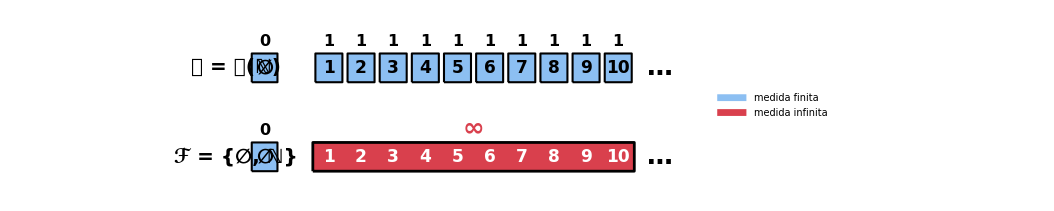

```mathematica
ClearAll[nTot,hC,colFin,colInf,y1,y2,celdaFina,celdaVacia,bloqueUnico,filaG,filaF,etiquetasFilas,grafico4,diagrama4];

nTot=10;hC=0.84;
colFin=RGBColor[0.55,0.75,0.95];   (*medida finita*)
colInf=RGBColor[0.85,0.25,0.3];    (*medida infinita*)
y1=0;y2=-2.6;

(*un elemento unipuntual {k}:su medida (el 1 de arriba) es finita*)
celdaFina[k_,y_]:={colFin,EdgeForm[{Black,AbsoluteThickness[1.5]}],Rectangle[{k-0.42,y},{k+0.42,y+hC},RoundingRadius->0.1],Black,Text[Style[k,17,Bold],{k,y+hC/2}],Text[Style["1",16,Bold],{k,y+hC+0.35}]};

celdaVacia[y_]:={colFin,EdgeForm[{Black,AbsoluteThickness[1.5]}],Rectangle[{-1.4,y},{-0.6,y+hC},RoundingRadius->0.1],Black,Text[Style["∅",20,Bold],{-1.0,y+hC/2}],Text[Style["0",16,Bold],{-1.0,y+hC+0.35}]};

(*el único elemento no vacío de la sigma-álgebra trivial:todo N en un solo bloque*)
bloqueUnico[y_]:={colInf,EdgeForm[{Black,AbsoluteThickness[2]}],Rectangle[{0.5,y},{nTot+0.5,y+hC},RoundingRadius->0.15],White,Table[Text[Style[k,17,Bold],{k,y+hC/2}],{k,1,nTot}],Text[Style["∞",26,Bold,colInf],{(nTot+1)/2,y+hC+0.4}]};

filaG={celdaVacia[y1],Table[celdaFina[k,y1],{k,1,nTot}],Black,Text[Style["…",26,Bold],{nTot+1.3,y1+hC/2}]};

filaF={celdaVacia[y2],bloqueUnico[y2],Black,Text[Style["…",26,Bold],{nTot+1.3,y2+hC/2}]};

etiquetasFilas={Black,Text[Style["𝒢 = 𝒫(ℕ)",20,Bold],{-1.9,y1+hC/2},{1,0}],Text[Style["ℱ = {∅, ℕ}",20,Bold],{-1.9,y2+hC/2},{1,0}]};

grafico4=Graphics[{filaG,filaF,etiquetasFilas},PlotRange->{{-6.4,nTot+2.2},{y2-0.6,y1+hC+1.0}},ImageSize->780];

diagrama4=Legended[grafico4,SwatchLegend[{colFin,colInf},{"medida finita","medida infinita"},LabelStyle->Directive[FontSize->17],LegendMarkerSize->20]];

diagrama4

Export["T2_P31_a.png",diagrama4,Background->None,ImageResolution->600];
```

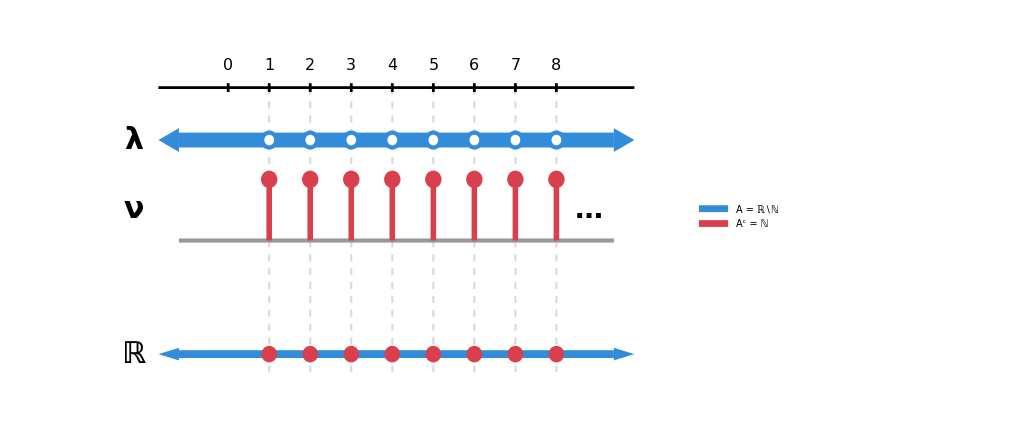

```mathematica
ClearAll[colLam,colN,nMax,xIzq,xDer,h,yEje,yLam,yNu,yPart,abierto,barraLam,guias,ejeReal,filaLam,filaNu,filaPart,grafico1,diagrama1];

colLam=RGBColor[0.2,0.55,0.85];   (*λ:vive en ℝ\ℕ*)
colN=RGBColor[0.85,0.25,0.3];     (*ν:vive en ℕ*)
nMax=8;xIzq=-1.2;xDer=9.4;
h=0.17;
yEje=1.2;yLam=0;yNu=-2.3;yPart=-4.9;

abierto[x_,y_,col_]:={White,Disk[{x,y},h],col,AbsoluteThickness[3],Circle[{x,y},h]};

(*barra con flechas en los dos extremos:la recta real completa*)
barraLam[y_,col_,alto_]:={col,Rectangle[{xIzq,y-alto},{xDer,y+alto}],Polygon[{{xIzq,y+1.6 alto},{xIzq,y-1.6 alto},{xIzq-0.5,y}}],Polygon[{{xDer,y+1.6 alto},{xDer,y-1.6 alto},{xDer+0.5,y}}]};

guias={GrayLevel[0.85],Dashed,AbsoluteThickness[1.5],Table[Line[{{k,yEje},{k,yPart-0.5}}],{k,1,nMax}]};

ejeReal={Black,AbsoluteThickness[2],Line[{{xIzq-0.5,yEje},{xDer+0.5,yEje}}],Table[{Line[{{k,yEje-0.1},{k,yEje+0.1}}],Text[Style[k,16],{k,yEje+0.5}]},{k,0,nMax}]};

(*λ:toda la recta salvo los puntos de N (huecos)*)
filaLam={barraLam[yLam,colLam,h],Table[abierto[k,yLam,colLam],{k,1,nMax}],{Black,Text[Style["λ",30,Bold],{xIzq-1.1,yLam}]}};

(*ν:masa 1 en cada punto de N,nada entre ellos*)
filaNu={GrayLevel[0.6],AbsoluteThickness[3],Line[{{xIzq,yNu},{xDer,yNu}}],Table[{colN,AbsoluteThickness[4],Line[{{k,yNu},{k,yNu+1.4}}],Disk[{k,yNu+1.4},0.2]},{k,1,nMax}],{Black,Text[Style["…",28,Bold],{nMax+0.8,yNu+0.7}],Text[Style["ν",30,Bold],{xIzq-1.1,yNu+0.7}]}};

(*la recta partida en A=ℝ\ℕ (azul) y ℕ (puntos rojos)*)
filaPart={barraLam[yPart,colLam,0.09],Table[{colN,Disk[{k,yPart},0.19]},{k,1,nMax}],{Black,Text[Style["ℝ",30,Bold],{xIzq-1.1,yPart}]}};

grafico1=Graphics[{guias,ejeReal,filaLam,filaNu,filaPart},PlotRange->{{xIzq-2.2,xDer+1.4},{yPart-0.9,yEje+1.1}},ImageSize->760];

diagrama1=Legended[grafico1,SwatchLegend[{colLam,colN},{"A = ℝ∖ℕ","Aᶜ = ℕ"},LabelStyle->Directive[FontSize->18],LegendMarkerSize->20]];

diagrama1

Export["T2_P32_a.png",diagrama1,Background->None,ImageResolution->600];
```

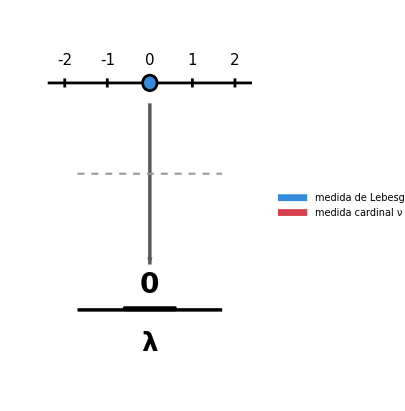
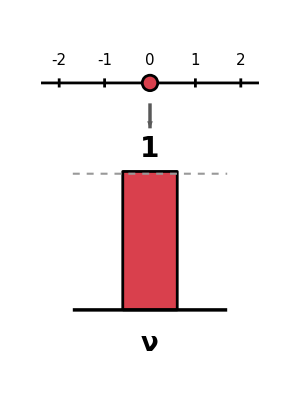
A = {0}
-Graphics--Graphics-

```mathematica
ClearAll[colLam,colN,panelMedida,panelLam,panelNu,diagrama2];

colLam=RGBColor[0.2,0.55,0.85];
colN=RGBColor[0.85,0.25,0.3];

(*valor=medida del conjunto {0};la altura de la barra es proporcional a ese valor*)
panelMedida[col_,valor_,titulo_]:=Graphics[{(*recta real con el punto 0 destacado*){Black,AbsoluteThickness[2],Line[{{-2.4,5},{2.4,5}}]},Table[{Black,AbsoluteThickness[2],Line[{{k,4.9},{k,5.1}}],Text[Style[k,15],{k,5.5}]},{k,-2,2}],{col,EdgeForm[{Black,AbsoluteThickness[2]}],Disk[{0,5},0.17]},(*flecha desde el punto hasta su medida*){GrayLevel[0.35],AbsoluteThickness[2.5],Arrowheads[0.07],Arrow[{{0,4.55},{0,3 valor+1.0}}]},(*barra de la medida,con una línea discontinua a la altura 1*){col,EdgeForm[{Black,AbsoluteThickness[2]}],Rectangle[{-0.6,0},{0.6,3 valor+0.05}]},{GrayLevel[0.6],Dashed,AbsoluteThickness[1.5],Line[{{-1.7,3},{1.7,3}}]},{Black,AbsoluteThickness[2.5],Line[{{-1.7,0},{1.7,0}}]},Text[Style[valor,28,Bold],{0,3 valor+0.55}],Text[Style[titulo,26,Bold],{0,-0.75}]},PlotRange->{{-2.7,2.7},{-1.4,6.0}},ImageSize->300];

panelLam=panelMedida[colLam,0,"λ"];
panelNu=panelMedida[colN,1,"ν"];

diagrama2=Legended[Column[{Style["A = {0}",24,Bold],Row[{panelLam,Spacer[40],panelNu}]},Alignment->Center,Spacings->0.8],SwatchLegend[{colLam,colN},{"medida de Lebesgue λ","medida cardinal ν"},LabelStyle->Directive[FontSize->18],LegendMarkerSize->20]];

diagrama2

Export["T2_P33_a.png",diagrama2,Background->None,ImageResolution->600];
```

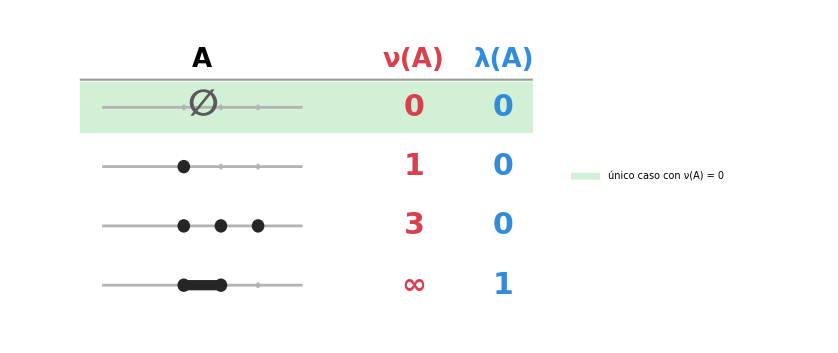

```mathematica
ClearAll[colLam,colN,colA,colOk,dy,xN,xL,yy,base,icono,valoresNu,valoresLam,fila,cabecera,destacado,grafico3,diagrama3];

colLam=RGBColor[0.2,0.55,0.85];
colN=RGBColor[0.85,0.25,0.3];
colA=GrayLevel[0.15];                  (*el conjunto A dibujado en la recta*)
colOk=RGBColor[0.82,0.94,0.84];
dy=1.5;xN=6.2;xL=8.6;

yy[i_]:=-(i-1) dy;

base[y_]:={GrayLevel[0.7],AbsoluteThickness[2],Line[{{-2.2,y},{3.2,y}}],Table[Line[{{k,y-0.07},{k,y+0.07}}],{k,0,2}]};

(*cuatro conjuntos de ejemplo:vacío,un punto,tres puntos,un intervalo*)
icono[1,y_]:={base[y],Text[Style["∅",36,Bold,GrayLevel[0.35]],{0.5,y+0.05}]};
icono[2,y_]:={base[y],colA,Disk[{0,y},0.17]};
icono[3,y_]:={base[y],colA,Table[Disk[{k,y},0.17],{k,0,2}]};
icono[4,y_]:={base[y],colA,Rectangle[{0,y-0.13},{1,y+0.13}],Disk[{0,y},0.17],Disk[{1,y},0.17]};

valoresNu={"0","1","3","∞"};
valoresLam={"0","0","0","1"};

cabecera={Text[Style["A",26,Bold],{0.5,1.2}],Text[Style["ν(A)",26,Bold,colN],{xN,1.2}],Text[Style["λ(A)",26,Bold,colLam],{xL,1.2}],{GrayLevel[0.6],AbsoluteThickness[1.5],Line[{{-2.8,0.7},{9.4,0.7}}]}};

(*se resalta la única fila con ν(A)=0*)
destacado={colOk,EdgeForm[None],Rectangle[{-2.8,yy[1]-0.65},{9.4,yy[1]+0.65},RoundingRadius->0.2]};

fila[i_]:={icono[i,yy[i]],Text[Style[valoresNu[[i]],30,Bold,colN],{xN,yy[i]}],Text[Style[valoresLam[[i]],30,Bold,colLam],{xL,yy[i]}]};

grafico3=Graphics[{destacado,cabecera,Table[fila[i],{i,1,4}]},PlotRange->{{-3,9.8},{yy[4]-0.9,1.9}},ImageSize->620];

diagrama3=Legended[grafico3,SwatchLegend[{colOk},{"único caso con ν(A) = 0"},LabelStyle->Directive[FontSize->18],LegendMarkerSize->20]];

diagrama3

Export["T2_P33_b.png",diagrama3,Background->None,ImageResolution->600];
```

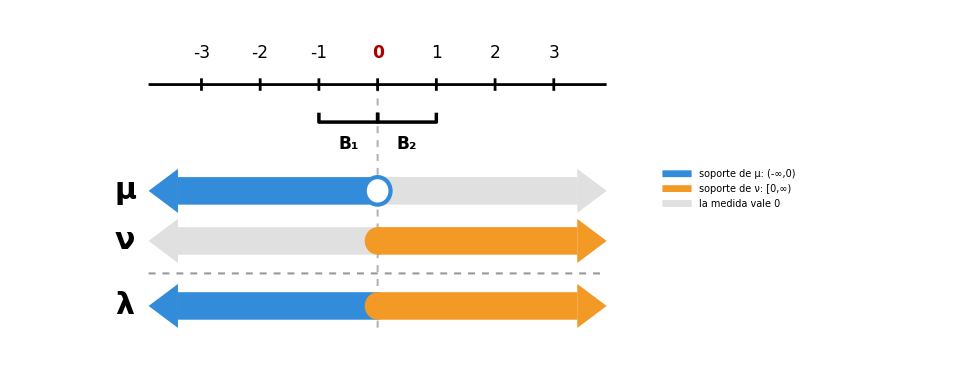

```mathematica
ClearAll[limX,sep,h,yEje,yMu,yNu,ySep,yLam,colMu,colNu,colNulo,abierto,cerrado,barra,flechaIzq,flechaDer,ejeReal,marcasB,filaMu,filaNu,filaLam,separador,guia,etiquetasFilas,grafico1,diagrama1];

limX=3.4;sep=0.8;h=0.22;
yEje=1.7;yMu=0;yNu=-sep;ySep=-1.65 sep;yLam=-2.3 sep;

colMu=RGBColor[0.2,0.55,0.85];    (*μ:vive en ℝ⁻=(-∞,0)*)
colNu=RGBColor[0.95,0.6,0.15];    (*ν:vive en ℝ⁺=[0,∞)*)
colNulo=GrayLevel[0.88];            (*zona donde esa medida vale 0*)

abierto[x_,y_,col_]:={White,Disk[{x,y},h],col,AbsoluteThickness[3],Circle[{x,y},h]};
cerrado[x_,y_,col_]:={col,Disk[{x,y},h]};
barra[x1_,x2_,y_,col_]:={col,Rectangle[{x1,y-h},{x2,y+h}]};
flechaIzq[y_,col_]:={col,Polygon[{{-limX,y+1.6 h},{-limX,y-1.6 h},{-limX-0.5,y}}]};
flechaDer[y_,col_]:={col,Polygon[{{limX,y+1.6 h},{limX,y-1.6 h},{limX+0.5,y}}]};

(*eje real con el 0 destacado*)
ejeReal={Black,AbsoluteThickness[2],Line[{{-limX-0.5,yEje},{limX+0.5,yEje}}],Table[Line[{{k,yEje-0.1},{k,yEje+0.1}}],{k,-3,3}],Table[Text[Style[k,17,If[k==0,Bold,Plain],If[k==0,Darker[Red],Black]],{k,yEje+0.5}],{k,-3,3}]};

(*los intervalos B1=(-1,0) y B2=(0,1) de los contraejemplos*)
marcasB={Black,AbsoluteThickness[2.5],Line[{{-1,yEje-0.45},{-1,yEje-0.6},{0,yEje-0.6},{0,yEje-0.45}}],Line[{{0,yEje-0.45},{0,yEje-0.6},{1,yEje-0.6},{1,yEje-0.45}}],Text[Style[Subscript["B",1],17,Bold],{-0.5,yEje-0.95}],Text[Style[Subscript["B",2],17,Bold],{0.5,yEje-0.95}]};

guia={GrayLevel[0.7],Dashed,AbsoluteThickness[1.5],Line[{{0,yEje},{0,yLam-0.45}}]};

(*μ vive solo a la izquierda del 0;el 0 no pertenece a ℝ⁻ (círculo hueco)*)
filaMu={barra[-limX,0,yMu,colMu],flechaIzq[yMu,colMu],barra[0,limX,yMu,colNulo],flechaDer[yMu,colNulo],abierto[0,yMu,colMu]};

(*ν vive solo a la derecha del 0;el 0 sí pertenece a ℝ⁺ (punto macizo)*)
filaNu={barra[-limX,0,yNu,colNulo],flechaIzq[yNu,colNulo],barra[0,limX,yNu,colNu],flechaDer[yNu,colNu],cerrado[0,yNu,colNu]};

separador={GrayLevel[0.6],Dashed,AbsoluteThickness[1.5],Line[{{-limX-0.5,ySep},{limX+0.5,ySep}}]};

(*λ=μ+ν:las dos mitades juntas cubren toda la recta*)
filaLam={barra[-limX,0,yLam,colMu],flechaIzq[yLam,colMu],barra[0,limX,yLam,colNu],flechaDer[yLam,colNu],cerrado[0,yLam,colNu]};

etiquetasFilas={Black,Text[Style["μ",30,Bold],{-limX-0.9,yMu}],Text[Style["ν",30,Bold],{-limX-0.9,yNu}],Text[Style["λ",30,Bold],{-limX-0.9,yLam}]};

grafico1=Graphics[{guia,ejeReal,marcasB,filaMu,filaNu,separador,filaLam,etiquetasFilas},PlotRange->{{-limX-1.6,limX+1.0},{yLam-0.6,yEje+0.8}},ImageSize->720];

diagrama1=Legended[grafico1,SwatchLegend[{colMu,colNu,colNulo},{"soporte de μ: (-∞,0)","soporte de ν: [0,∞)","la medida vale 0"},LabelStyle->Directive[FontSize->18],LegendMarkerSize->20]];

diagrama1

Export["T2_P34_a.png",diagrama1,Background->None,ImageResolution->600];
```

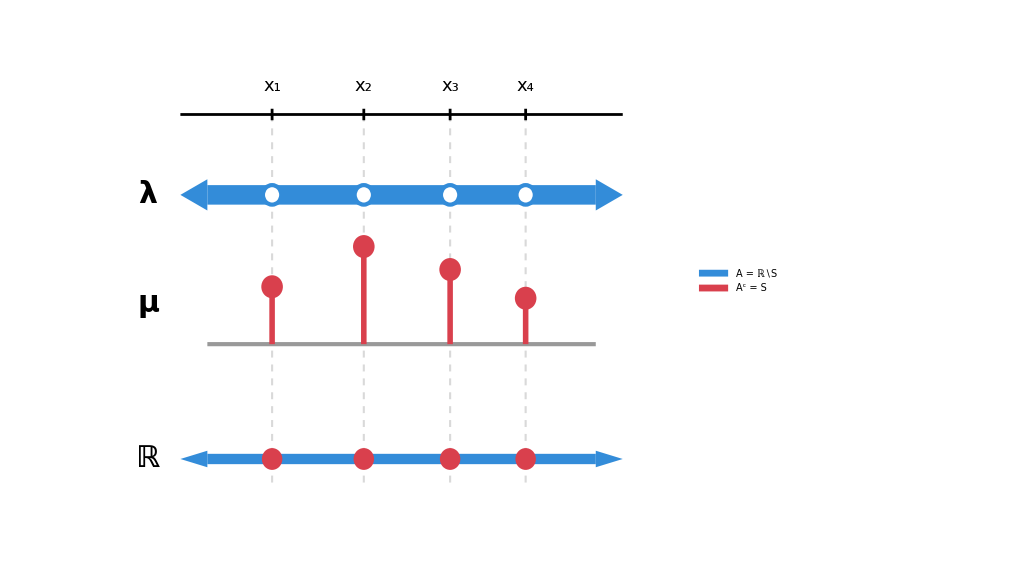

```mathematica
ClearAll[xs,alturas,limX,h,colLam,colMu,yEje,yLam,yMu,yPart,abierto,barraLam,guias,ejeReal,filaLam,filaMu,filaPart,grafico2,diagrama2];

xs={-2.4,-0.7,0.9,2.3};          (*los puntos x_1,...,x_n del soporte*)
alturas={1.0,1.7,1.3,0.8};       (*masas arbitrarias,solo ilustrativas*)
limX=3.6;h=0.17;

colLam=RGBColor[0.2,0.55,0.85];   (*λ:vive en ℝ\S*)
colMu=RGBColor[0.85,0.25,0.3];    (*μ:vive en S*)
yEje=1.4;yLam=0;yMu=-2.6;yPart=-4.6;

abierto[x_,y_,col_]:={White,Disk[{x,y},h],col,AbsoluteThickness[3],Circle[{x,y},h]};

(*barra con flechas en los dos extremos:la recta real completa*)
barraLam[y_,col_,alto_]:={col,Rectangle[{-limX,y-alto},{limX,y+alto}],Polygon[{{-limX,y+1.6 alto},{-limX,y-1.6 alto},{-limX-0.5,y}}],Polygon[{{limX,y+1.6 alto},{limX,y-1.6 alto},{limX+0.5,y}}]};

guias={GrayLevel[0.85],Dashed,AbsoluteThickness[1.5],Table[Line[{{x,yEje},{x,yPart-0.5}}],{x,xs}]};

ejeReal={Black,AbsoluteThickness[2],Line[{{-limX-0.5,yEje},{limX+0.5,yEje}}],Table[{Line[{{xs[[i]],yEje-0.1},{xs[[i]],yEje+0.1}}],Text[Style[Subscript["x",i],18],{xs[[i]],yEje+0.5}]},{i,1,Length[xs]}]};

(*λ:toda la recta salvo los puntos de S (huecos)*)
filaLam={barraLam[yLam,colLam,h],Table[abierto[x,yLam,colLam],{x,xs}],{Black,Text[Style["λ",30,Bold],{-limX-1.1,yLam}]}};

(*μ:masa concentrada en cada x_i,nada entre ellos*)
filaMu={GrayLevel[0.6],AbsoluteThickness[3],Line[{{-limX,yMu},{limX,yMu}}],Table[{colMu,AbsoluteThickness[4],Line[{{xs[[i]],yMu},{xs[[i]],yMu+alturas[[i]]}}],Disk[{xs[[i]],yMu+alturas[[i]]},0.2]},{i,1,Length[xs]}],{Black,Text[Style["μ",30,Bold],{-limX-1.1,yMu+0.7}]}};

(*la recta partida en A=ℝ\S (azul) y S (puntos rojos)*)
filaPart={barraLam[yPart,colLam,0.09],Table[{colMu,Disk[{x,yPart},0.19]},{x,xs}],{Black,Text[Style["ℝ",30,Bold],{-limX-1.1,yPart}]}};

grafico2=Graphics[{guias,ejeReal,filaLam,filaMu,filaPart},PlotRange->{{-limX-2.2,limX+1.4},{yPart-0.9,yEje+1.1}},ImageSize->760];

diagrama2=Legended[grafico2,SwatchLegend[{colLam,colMu},{"A = ℝ∖S","Aᶜ = S"},LabelStyle->Directive[FontSize->18],LegendMarkerSize->20]];

diagrama2

Export["T2_P35_a.png",diagrama2,Background->None,ImageResolution->600];
```

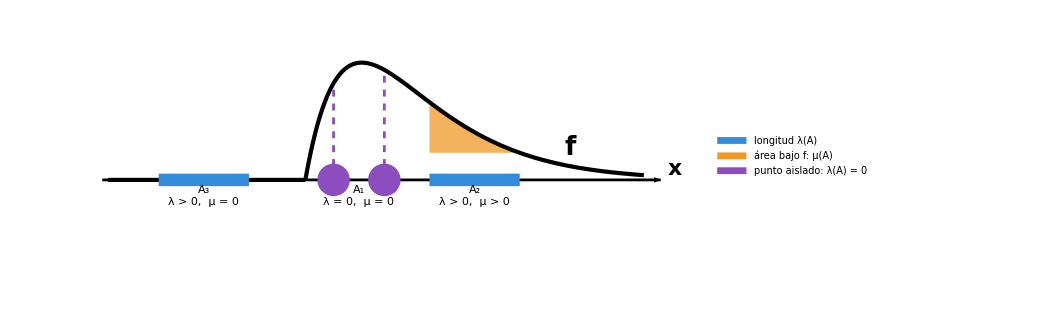

```mathematica
ClearAll[f,colLam,colMu,colNulo,ptsNulos,aI,bI,aC,bC,curva,areaPos,ejeX,barras,guias,puntos,etiqueta,etiquetas,grafico1,diagrama1];

f[x_]:=Piecewise[{{2 x Exp[-x],x>=0}},0];   (*densidad de ejemplo,nula en x<0*)

colLam=RGBColor[0.2,0.55,0.85];    (*longitud sobre el eje:λ(A)*)
colMu=RGBColor[0.95,0.6,0.15];     (*área bajo f:μ(A)*)
colNulo=RGBColor[0.55,0.3,0.75];   (*puntos aislados:λ(A)=0*)

ptsNulos={0.5,1.4};     (*conjunto finito de puntos*)
aI=2.2;bI=3.8;        (*intervalo donde f>0*)
aC=-2.6;bC=-1;        (*intervalo donde f=0*)

curva=Plot[f[x],{x,-3.5,6},PlotStyle->Directive[Black,AbsoluteThickness[3]],Axes->False];

areaPos=Plot[f[x],{x,aI,bI},Filling->Axis,FillingStyle->Directive[colMu,Opacity[0.75]],PlotStyle->Directive[Opacity[0]],Axes->False];

ejeX={Black,AbsoluteThickness[2],Arrowheads[0.025],Arrow[{{-3.6,0},{6.3,0}}]};

(*los dos intervalos tienen longitud positiva*)
barras={AbsoluteThickness[9],CapForm["Butt"],colLam,Line[{{aI,0},{bI,0}}],Line[{{aC,0},{bC,0}}]};

(*los puntos tienen ancho cero:la línea discontinua hasta la curva no encierra área*)
guias={colNulo,Dashed,AbsoluteThickness[2],Table[Line[{{x,0},{x,f[x]}}],{x,ptsNulos}]};
puntos={colNulo,PointSize[0.03],Point[{#,0}&/@ptsNulos]};

etiqueta[n_,xc_,txt_]:=Text[Column[{Style[Subscript["A",n],22,Bold],Style[txt,18]},Alignment->Center],{xc,-0.1},{0,1}];

etiquetas={etiqueta[1,Mean[ptsNulos],"λ = 0,  μ = 0"],etiqueta[2,(aI+bI)/2,"λ > 0,  μ > 0"],etiqueta[3,(aC+bC)/2,"λ > 0,  μ = 0"],Text[Style["f",26,Bold],{4.7,0.2}],Text[Style["x",22,Bold],{6.55,0.07}]};

grafico1=Show[areaPos,curva,Graphics[{ejeX,barras,guias,puntos,etiquetas}],PlotRange->{{-3.8,6.8},{-0.65,0.95}},PlotRangePadding->None,AspectRatio->0.4,ImageSize->780];

diagrama1=Legended[grafico1,SwatchLegend[{colLam,colMu,colNulo},{"longitud λ(A)","área bajo f: μ(A)","punto aislado: λ(A) = 0"},LabelStyle->Directive[FontSize->18],LegendMarkerSize->20]];

diagrama1

Export["T2_P36_a.png",diagrama1,Background->None,ImageResolution->600];
```

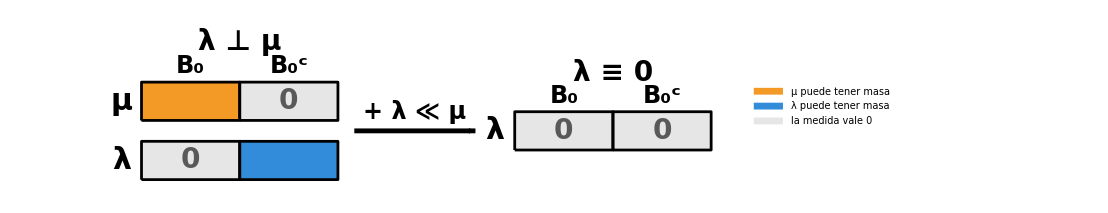

```mathematica
ClearAll[colLam,colMu,colNulo,ancho,alto,x0D,bloque,fila,cabeceras,flecha,titulos,etiquetasFilas,grafico2,diagrama2];

colLam=RGBColor[0.2,0.55,0.85];   (*λ puede tener masa*)
colMu=RGBColor[0.95,0.6,0.15];    (*μ puede tener masa*)
colNulo=GrayLevel[0.9];             (*la medida vale 0*)

ancho=3;alto=1.1;x0D=11.4;

(*un bloque de Ω:coloreado si la medida puede ser positiva,gris con un 0 si es nula*)
bloque[x0_,y0_,col_,nulo_]:={col,EdgeForm[{Black,AbsoluteThickness[2]}],Rectangle[{x0,y0},{x0+ancho,y0+alto}],If[nulo,Text[Style["0",28,Bold,GrayLevel[0.35]],{x0+ancho/2,y0+alto/2}],{}]};

(*una fila es Ω=B₀ ∪ B₀ᶜ:bloque izquierdo y bloque derecho*)
fila[x0_,y0_,colIzq_,nuloIzq_,colDer_,nuloDer_]:={bloque[x0,y0,colIzq,nuloIzq],bloque[x0+ancho,y0,colDer,nuloDer]};

cabeceras[x0_,y_]:={Black,Text[Style["B₀",24,Bold],{x0+ancho/2,y}],Text[Style["B₀ᶜ",24,Bold],{x0+3 ancho/2,y}]};

(*izquierda:lo que impone la singularidad.μ vive en B₀ y λ vive en B₀ᶜ*)
(*derecha:al añadir λ≪μ,el bloque de λ en B₀ᶜ también se anula*)
flecha={Black,AbsoluteThickness[3.5],Arrowheads[0.035],Arrow[{{2 ancho+0.5,1.4},{x0D-1.2,1.4}}],Text[Style["+ λ ≪ μ",24,Bold],{(2 ancho+0.5+x0D-1.2)/2,1.95}]};

titulos={Black,Text[Style["λ ⊥ μ",28,Bold],{ancho,3.95}],Text[Style["λ ≡ 0",28,Bold],{x0D+ancho,3.05}]};

etiquetasFilas={Black,Text[Style["μ",30,Bold],{-0.6,1.7+alto/2}],Text[Style["λ",30,Bold],{-0.6,alto/2}],Text[Style["λ",30,Bold],{x0D-0.6,0.85+alto/2}]};

grafico2=Graphics[{cabeceras[0,3.25],fila[0,1.7,colMu,False,colNulo,True],(*μ:masa en B₀,nula en B₀ᶜ*)fila[0,0,colNulo,True,colLam,False],(*λ:nula en B₀,masa posible en B₀ᶜ*)flecha,cabeceras[x0D,2.4],fila[x0D,0.85,colNulo,True,colNulo,True],(*λ final:nula en los dos bloques*)titulos,etiquetasFilas},PlotRange->{{-1.4,17.8},{-0.4,4.6}},ImageSize->820];

diagrama2=Legended[grafico2,SwatchLegend[{colMu,colLam,colNulo},{"μ puede tener masa","λ puede tener masa","la medida vale 0"},LabelStyle->Directive[FontSize->18],LegendMarkerSize->20]];

diagrama2

Export["T2_P37_a.png",diagrama2,Background->None,ImageResolution->600];
```

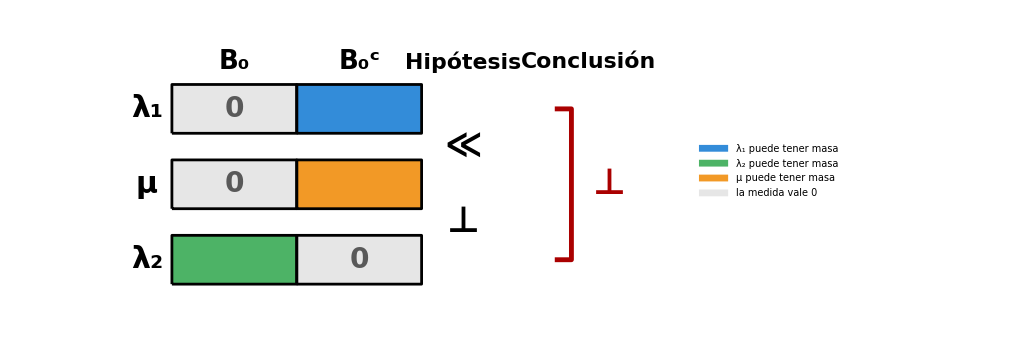

```mathematica
ClearAll[colL1,colL2,colMu,colNulo,ancho,alto,dy,yF,centro,bloque,fila,yCab,xS,xC,cabeceras,simbolos,conclusion,etiquetasFilas,grafico1,diagrama1];

colL1=RGBColor[0.2,0.55,0.85];    (*λ₁*)
colL2=RGBColor[0.3,0.7,0.4];      (*λ₂*)
colMu=RGBColor[0.95,0.6,0.15];    (*μ*)
colNulo=GrayLevel[0.9];             (*la medida vale 0*)

ancho=3;alto=1.1;dy=1.7;
yF[i_]:=-(i-1) dy;                (*filas de arriba abajo:λ₁,μ,λ₂*)
centro[i_]:=yF[i]+alto/2;

bloque[x0_,i_,col_,nulo_]:={col,EdgeForm[{Black,AbsoluteThickness[2]}],Rectangle[{x0,yF[i]},{x0+ancho,yF[i]+alto}],If[nulo,Text[Style["0",28,Bold,GrayLevel[0.35]],{x0+ancho/2,centro[i]}],{}]};

fila[i_,colIzq_,nuloIzq_,colDer_,nuloDer_]:={bloque[0,i,colIzq,nuloIzq],bloque[ancho,i,colDer,nuloDer]};

yCab=yF[1]+alto+0.5;
xS=2 ancho+1.0;     (*columna de las hipótesis*)
xC=2 ancho+3.6;     (*columna de la conclusión*)

cabeceras={Black,Text[Style["B₀",26,Bold],{ancho/2,yCab}],Text[Style["B₀ᶜ",26,Bold],{3 ancho/2,yCab}],Text[Style["Hipótesis",22,Bold],{xS,yCab}],Text[Style["Conclusión",22,Bold],{xC+0.4,yCab}]};

(*hipótesis:λ₁≪μ (filas 1 y 2) y μ⊥λ₂ (filas 2 y 3)*)
simbolos={Black,Text[Style["≪",36,Bold],{xS,(centro[1]+centro[2])/2}],Text[Style["⊥",36,Bold],{xS,(centro[2]+centro[3])/2}]};

(*conclusión:λ₁⊥λ₂ (filas 1 y 3)*)
conclusion={Darker[Red],AbsoluteThickness[3.5],Line[{{xC-0.4,centro[1]},{xC,centro[1]},{xC,centro[3]},{xC-0.4,centro[3]}}],Text[Style["⊥",36,Bold,Darker[Red]],{xC+0.9,centro[2]}]};

etiquetasFilas={Black,Text[Style["λ₁",30,Bold],{-0.6,centro[1]},{1,0}],Text[Style["μ",30,Bold],{-0.6,centro[2]},{1,0}],Text[Style["λ₂",30,Bold],{-0.6,centro[3]},{1,0}]};

grafico1=Graphics[{cabeceras,fila[1,colNulo,True,colL1,False],(*λ₁ se anula en B₀ porque μ se anula ahí*)fila[2,colNulo,True,colMu,False],(*μ:nula en B₀,masa en B₀ᶜ*)fila[3,colL2,False,colNulo,True],(*λ₂:masa en B₀,nula en B₀ᶜ*)simbolos,conclusion,etiquetasFilas},PlotRange->{{-2,xC+2.4},{yF[3]-0.6,yCab+0.7}},ImageSize->760];

diagrama1=Legended[grafico1,SwatchLegend[{colL1,colL2,colMu,colNulo},{"λ₁ puede tener masa","λ₂ puede tener masa","μ puede tener masa","la medida vale 0"},LabelStyle->Directive[FontSize->18],LegendMarkerSize->20]];

diagrama1

Export["T2_P38_a.png",diagrama1,Background->None,ImageResolution->600];
```

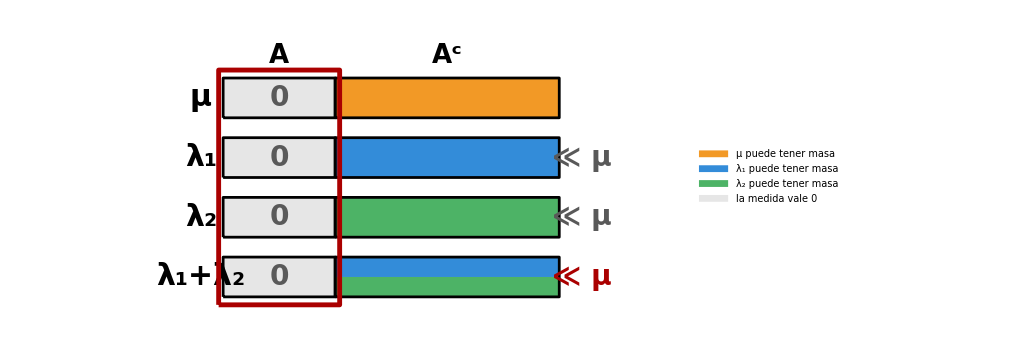

```mathematica
ClearAll[colL1,colL2,colMu,colNulo,wA,wR,alto,dy,yF,centro,bloque,filaSimple,filaSuma,marcoA,yCab,cabeceras,etiquetasFilas,relaciones,grafico2,diagrama2];

colL1=RGBColor[0.2,0.55,0.85];
colL2=RGBColor[0.3,0.7,0.4];
colMu=RGBColor[0.95,0.6,0.15];
colNulo=GrayLevel[0.9];

wA=3;wR=6;alto=1.0;dy=1.5;
yF[i_]:=-(i-1) dy;          (*filas:μ,λ₁,λ₂,λ₁+λ₂*)
centro[i_]:=yF[i]+alto/2;

bloque[x0_,w_,i_,col_,nulo_]:={col,EdgeForm[{Black,AbsoluteThickness[2]}],Rectangle[{x0,yF[i]},{x0+w,yF[i]+alto}],If[nulo,Text[Style["0",28,Bold,GrayLevel[0.35]],{x0+w/2,centro[i]}],{}]};

(*columna A (μ(A)=0):todas las medidas valen 0;columna Aᶜ:pueden tener masa*)
filaSimple[i_,colRest_]:={bloque[0,wA,i,colNulo,True],bloque[wA,wR,i,colRest,False]};

(*la suma se dibuja con dos mitades apiladas:la masa de λ₁ y la de λ₂*)
filaSuma[i_]:={bloque[0,wA,i,colNulo,True],colL1,EdgeForm[None],Rectangle[{wA,yF[i]+alto/2},{wA+wR,yF[i]+alto}],colL2,Rectangle[{wA,yF[i]},{wA+wR,yF[i]+alto/2}],FaceForm[None],EdgeForm[{Black,AbsoluteThickness[2]}],Rectangle[{wA,yF[i]},{wA+wR,yF[i]+alto}]};

(*el conjunto A,de μ-medida nula,atraviesa todas las filas*)
marcoA={FaceForm[None],EdgeForm[{Darker[Red],Dashed,AbsoluteThickness[3.5]}],Rectangle[{-0.12,yF[4]-0.2},{wA+0.12,yF[1]+alto+0.2},RoundingRadius->0.15]};

yCab=yF[1]+alto+0.55;
cabeceras={Black,Text[Style["A",26,Bold],{wA/2,yCab}],Text[Style["Aᶜ",26,Bold],{wA+wR/2,yCab}]};

etiquetasFilas={Black,Text[Style["μ",30,Bold],{-0.6,centro[1]},{1,0}],Text[Style["λ₁",30,Bold],{-0.6,centro[2]},{1,0}],Text[Style["λ₂",30,Bold],{-0.6,centro[3]},{1,0}],Text[Style["λ₁+λ₂",30,Bold],{-0.6,centro[4]},{1,0}]};

(*hipótesis en gris,conclusión en rojo*)
relaciones={Text[Style["≪ μ",28,Bold,GrayLevel[0.35]],{wA+wR+0.6,centro[2]},{-1,0}],Text[Style["≪ μ",28,Bold,GrayLevel[0.35]],{wA+wR+0.6,centro[3]},{-1,0}],Text[Style["≪ μ",28,Bold,Darker[Red]],{wA+wR+0.6,centro[4]},{-1,0}]};

grafico2=Graphics[{filaSimple[1,colMu],filaSimple[2,colL1],filaSimple[3,colL2],filaSuma[4],marcoA,cabeceras,relaciones,etiquetasFilas},PlotRange->{{-3.6,wA+wR+3.0},{yF[4]-0.6,yCab+0.6}},ImageSize->760];

diagrama2=Legended[grafico2,SwatchLegend[{colMu,colL1,colL2,colNulo},{"μ puede tener masa","λ₁ puede tener masa","λ₂ puede tener masa","la medida vale 0"},LabelStyle->Directive[FontSize->18],LegendMarkerSize->20]];

diagrama2

Export["T2_P38_b.png",diagrama2,Background->None,ImageResolution->600];
```

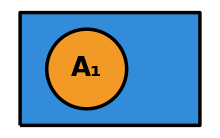
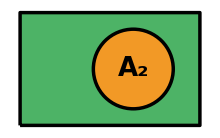
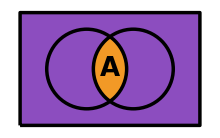
λ₁ ⊥ μ
-Graphics- | ∧ | λ₂ ⊥ μ
-Graphics- | ⇒ | λ₁+λ₂ ⊥ μ
-Graphics-

```mathematica
ClearAll[x,y,colL1,colL2,colMu,colSum,c1V,c2V,rV,limXV,limYV,fondo,borde,panel1,panel2,panel3,conTitulo,signo,cuerpo,leyenda,diagrama3];

colL1=RGBColor[0.2,0.55,0.85];
colL2=RGBColor[0.3,0.7,0.4];
colMu=RGBColor[0.95,0.6,0.15];
colSum=RGBColor[0.55,0.3,0.75];

c1V={-0.7,0};c2V={0.7,0};rV=1.2;limXV=2.7;limYV=1.7;

fondo[col_]:={col,Rectangle[{-limXV,-limYV},{limXV,limYV}]};
borde={FaceForm[None],EdgeForm[{Black,AbsoluteThickness[2.5]}],Rectangle[{-limXV,-limYV},{limXV,limYV}]};

(*λ₁⊥μ con A₁:μ vive dentro de A₁ y λ₁ fuera*)
panel1=Graphics[{fondo[colL1],colMu,Disk[c1V,rV],Black,AbsoluteThickness[2.5],Circle[c1V,rV],Text[Style["A₁",26,Bold],c1V],borde},PlotRange->{{-limXV,limXV},{-limYV,limYV}},ImageSize->220];

(*λ₂⊥μ con A₂:μ vive dentro de A₂ y λ₂ fuera*)
panel2=Graphics[{fondo[colL2],colMu,Disk[c2V,rV],Black,AbsoluteThickness[2.5],Circle[c2V,rV],Text[Style["A₂",26,Bold],c2V],borde},PlotRange->{{-limXV,limXV},{-limYV,limYV}},ImageSize->220];

(*conclusión con A=A₁∩A₂:μ vive en la lente y λ₁+λ₂ vive fuera de ella*)
panel3=Show[Graphics[fondo[colSum]],RegionPlot[(x+0.7)^2+y^2<1.44&&(x-0.7)^2+y^2<1.44,{x,-limXV,limXV},{y,-limYV,limYV},PlotStyle->Directive[colMu,Opacity[1]],BoundaryStyle->None,PlotPoints->60,MaxRecursion->3],Graphics[{Black,AbsoluteThickness[2.5],Circle[c1V,rV],Circle[c2V,rV],Text[Style["A",26,Bold],{0,0}],borde}],PlotRange->{{-limXV,limXV},{-limYV,limYV}},AspectRatio->Automatic,Frame->False,Axes->False,ImageSize->220];

conTitulo[g_,txt_]:=Column[{Style[txt,24,Bold],g},Alignment->Center,Spacings->0.4];
signo[s_]:=Style[s,34,Bold,GrayLevel[0.35]];

cuerpo=Grid[{{conTitulo[panel1,"λ₁ ⊥ μ"],signo["∧"],conTitulo[panel2,"λ₂ ⊥ μ"],signo["⇒"],conTitulo[panel3,"λ₁+λ₂ ⊥ μ"]}},Alignment->{Center,Center},Spacings->{1.2,0}];

leyenda=SwatchLegend[{colMu,colL1,colL2,colSum},{"μ puede tener masa","λ₁ puede tener masa","λ₂ puede tener masa","λ₁+λ₂ puede tener masa"},LabelStyle->Directive[FontSize->18],LegendMarkerSize->20];

diagrama3=Legended[cuerpo,leyenda];

diagrama3

Export["T2_P38_c.png",diagrama3,Background->None,ImageResolution->600];
```

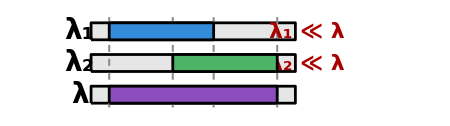
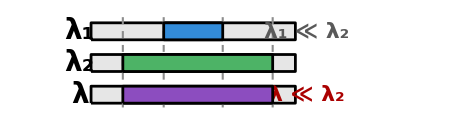
Caso general
-Graphics-Si λ₁ ≪ λ₂
-Graphics-

```mathematica
ClearAll[colL1,colL2,colSum,colNulo,wO,h,dy,yF,centro,barra,panelD,panelIzq,panelDer,leyenda,diagrama4];

colL1=RGBColor[0.2,0.55,0.85];
colL2=RGBColor[0.3,0.7,0.4];
colSum=RGBColor[0.55,0.3,0.75];
colNulo=GrayLevel[0.9];

wO=9;h=0.75;dy=1.4;
yF[i_]:=-(i-1) dy;           (*filas:λ₁,λ₂,λ=λ₁+λ₂*)
centro[i_]:=yF[i]+h/2;

barra[a_,b_,i_,col_]:={col,EdgeForm[{Black,AbsoluteThickness[2]}],Rectangle[{a,yF[i]},{b,yF[i]+h}]};

(*s1,s2:tramos de Ω donde λ₁ y λ₂ pueden tener masa.λ=λ₁+λ₂ tiene masa donde la tenga alguna de las dos:la unión de los tramos (aquí los tramos se solapan,así que la unión es un único tramo)*)
panelD[s1_,s2_,notas_,titulo_]:=Module[{su,guias},su={Min[s1[[1]],s2[[1]]],Max[s1[[2]],s2[[2]]]};
guias={GrayLevel[0.55],Dashed,AbsoluteThickness[1.5],Table[Line[{{xx,yF[1]+h+0.25},{xx,yF[3]-0.25}}],{xx,DeleteDuplicates[Flatten[{s1,s2}]]}]};
Column[{Style[titulo,22,Bold],Graphics[{Table[barra[0,wO,i,colNulo],{i,1,3}],guias,barra[s1[[1]],s1[[2]],1,colL1],barra[s2[[1]],s2[[2]],2,colL2],barra[su[[1]],su[[2]],3,colSum],Black,Text[Style["λ₁",28,Bold],{-0.5,centro[1]},{1,0}],Text[Style["λ₂",28,Bold],{-0.5,centro[2]},{1,0}],Text[Style["λ",28,Bold],{-0.5,centro[3]},{1,0}],Table[Text[Style[nota[[2]],22,Bold,nota[[3]]],{wO+0.5,centro[nota[[1]]]},{-1,0}],{nota,notas}]},PlotRange->{{-2.2,wO+5},{yF[3]-0.5,yF[1]+h+0.5}},ImageSize->450]},Alignment->Center,Spacings->0.6]];

(*caso general:λ₁≪λ y λ₂≪λ,porque cada tramo cabe en la unión*)
panelIzq=panelD[{0.8,5.4},{3.6,8.2},{{1,"λ₁ ≪ λ",Darker[Red]},{2,"λ₂ ≪ λ",Darker[Red]}},"Caso general"];

(*si λ₁≪λ₂,el tramo de λ₁ cae dentro del de λ₂ y la unión coincide con él*)
panelDer=panelD[{3.2,5.8},{1.4,8.0},{{1,"λ₁ ≪ λ₂",GrayLevel[0.35]},{3,"λ ≪ λ₂",Darker[Red]}},"Si λ₁ ≪ λ₂"];

leyenda=SwatchLegend[{colL1,colL2,colSum,colNulo},{"λ₁ puede tener masa","λ₂ puede tener masa","λ = λ₁+λ₂ puede tener masa","la medida vale 0"},LabelStyle->Directive[FontSize->18],LegendMarkerSize->20];

diagrama4=Legended[Row[{panelIzq,Spacer[30],panelDer}],leyenda];

diagrama4

Export["T2_P38_d.png",diagrama4,Background->None,ImageResolution->600];
```